## Square Lattice Phase diagram

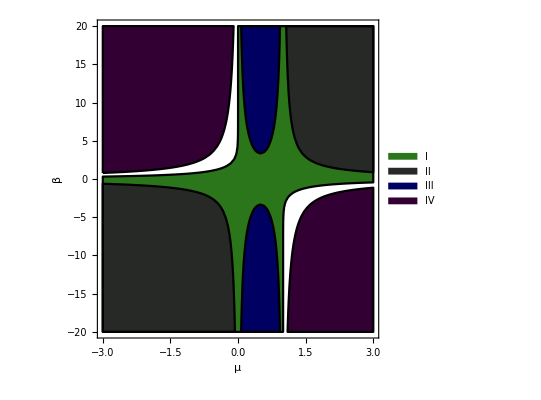

```mathematica
percplt=RegionPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.407,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274},{μ,-3,3},{β,-20,20},PlotLegends->{"I","II","III","IV"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotStyle->{RGBColor[0.17,0.46,0.1],RGBColor[0.15,0.16,0.15],RGBColor[0,0,0.39],RGBColor[0.2,0,0.2]},BoundaryStyle->Black]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","percplt.png"}],percplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\percplt.png

### PT junk

```mathematica
Solve[P==T(Log[1+Exp[μ/T]]+Log[1+Exp[(μ-1)/T]]),μ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→T Log[1/2 (-1-ⅇ^(1/T)-√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]},{μ→T Log[1/2 (-1-ⅇ^(1/T)+√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]}}

```mathematica
Simplify[{1/2 (2-1/(1+ⅇ^(μ/T))-ⅇ^(1/T)/(ⅇ^(1/T)+ⅇ^(μ/T)))>0.250368,ⅇ^((8 μ)/T)/((1+ⅇ^(μ/T))^4 (ⅇ^(1/T)+ⅇ^(μ/T))^4)>0.407,1. (1.125+1. Cosh[1/T]+0.0625 Cosh[2/T]) Sech[(-1+μ)/(2 T)]^4 Sech[μ/(2 T)]^4>3.256,1/((1+ⅇ^((-1+μ)/T))^4 (1+ⅇ^(μ/T))^4)>0.59274}/.{μ->T Log[1/2 (-1-ⅇ^(1/T)+√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]}]
```

{1/4 ⅇ^(-(1+P)/T) (1+ⅇ^(2/T)+4 ⅇ^((1+P)/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))-ⅇ^(1/T) (2+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))))>0.250368,1/256 ⅇ^(-(4 (1+P))/T) (1+ⅇ^(1/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))^8>0.407,1. (1.125+1. Cosh[1/T]+0.0625 Cosh[2/T]) Sech[1/2 (1/T-Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))])]^4 Sech[1/2 Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))]]^4>3.256,ⅇ^(-(4 P)/T)>0.59274}

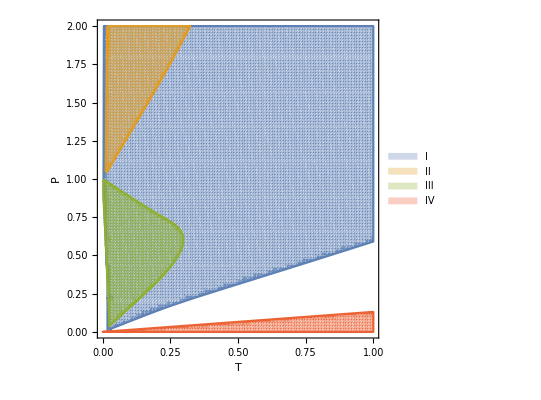

```mathematica
Quiet@RegionPlot[{1/4 ⅇ^(-(1+P)/T) (1+ⅇ^(2/T)+4 ⅇ^((1+P)/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))-ⅇ^(1/T) (2+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))))>0.250368,1/256 ⅇ^(-(4 (1+P))/T) (1+ⅇ^(1/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))^8>0.407,1. (1.125+1. Cosh[1/T]+0.0625 Cosh[2/T]) Sech[1/2 (1/T-Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))])]^4 Sech[1/2 Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))]]^4>3.256,ⅇ^(-(4 P)/T)>0.59274},{T,0,1},{P,0,2},PlotLegends->{"I","II","III","IV"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"T","P"},PlotPoints->100]
```

```mathematica
Simplify[{(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274,Not[(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274||(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274],(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.59274,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407}/.{β->1/T,μ->T Log[1/2 (-1-ⅇ^(1/T)+√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]}]
```

{ⅇ^(-(4 P)/T)>0.59274,ⅇ^(-(4 P)/T)≤0.59274,1/4 ⅇ^(-(1+P)/T) (1+ⅇ^(2/T)+4 ⅇ^((1+P)/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))-ⅇ^(1/T) (2+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))))>0.250368,1. (1.125+1. Cosh[1/T]+0.0625 Cosh[2/T]) Sech[1/2 (1/T-Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))])]^4 Sech[1/2 Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))]]^4>4.74192,1/256 ⅇ^(-(4 (1+P))/T) (1+ⅇ^(1/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))^8>0.407}

```mathematica
RegionPlot[{ⅇ^(-(4 P)/T)>0.59274,ⅇ^(-(4 P)/T)≤0.59274,1/4 ⅇ^(-(1+P)/T) (1+ⅇ^(2/T)+4 ⅇ^((1+P)/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))-ⅇ^(1/T) (2+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T))))>0.250368,1. (1.125+1. Cosh[1/T]+0.0625 Cosh[2/T]) Sech[1/2 (1/T-Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))])]^4 Sech[1/2 Log[1/2 (-1-ⅇ^(1/T)+√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))]]^4>4.74192,1/256 ⅇ^(-(4 (1+P))/T) (1+ⅇ^(1/T)-√(1-2 ⅇ^(1/T)+ⅇ^(2/T)+4 ⅇ^((1+P)/T)))^8>0.407},{T,0,1},{P,0,2},BoundaryStyle->Black,PlotLegends->{"Completely Disconnected phase","Minimally Disconnected phase","Amorphous graph phase","Lattice graph phase","Degenerate lattice graph phase"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"T","P"},PlotStyle->{RGBColor[0.2,0,0.2],RGBColor[0.28,0.11,0.15],RGBColor[0.17,0.46,0.1],RGBColor[0,0,0.39],RGBColor[0.15,0.16,0.15]},PlotPoints->200]
```

General::munfl: Exp[-198803.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795213.] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

### Th phases

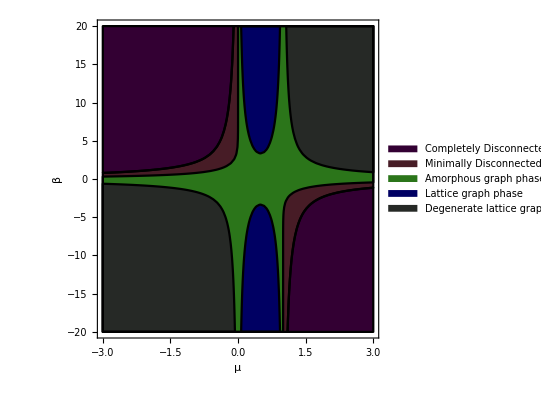

```mathematica
thphaseplt=RegionPlot[{(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274,Not[(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274||(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274],(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.407,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407},{μ,-3,3},{β,-20,20},BoundaryStyle->Black,PlotLegends->{"Completely Disconnected phase","Minimally Disconnected phase","Amorphous graph phase","Lattice graph phase","Degenerate lattice graph phase"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotStyle->{RGBColor[0.2,0,0.2],RGBColor[0.28,0.11,0.15],RGBColor[0.17,0.46,0.1],RGBColor[0,0,0.39],RGBColor[0.15,0.16,0.15]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","thphaseplt.png"}],thphaseplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\thphaseplt.png

```mathematica
dots=Show[ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"negBondPercolation.csv"}]],DataRange->{-3,-0.05},PlotRange->All,ImageSize->400,PlotStyle->Red,Frame->True,FrameLabel->{"μ","β"},LabelStyle->Directive[Bold,16],PlotLegends->{"Estimation of percolation I threshold from simulations"}],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"BondPercolation.csv"}]],DataRange->{1.05,3},PlotRange->All,ImageSize->400,PlotStyle->Red,Frame->True],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"neg8SitePercolation.csv"}]],DataRange->{-3,-0.05},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[0.09,0.87,1],Frame->True,FrameLabel->{"μ","β"},LabelStyle->Directive[Bold,16],PlotLegends->{"Estimation of percolation II threshold from simulations"}],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"8SitePercolation.csv"}]],DataRange->{1.05,3},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[0.09,0.87,1],Frame->True],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"neg4SitePercolation.csv"}]],DataRange->{0.05,0.95},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[0.7,1,0],Frame->True,FrameLabel->{"μ","β"},LabelStyle->Directive[Bold,16],PlotLegends->{"Estimation of percolation III threshold from simulations"}],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"4SitePercolation.csv"}]],DataRange->{0.05,0.95},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[0.7,1,0],Frame->True],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"neg0SitePercolation.csv"}]],DataRange->{-3,-0.05},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[1,0.35,0],Frame->True,FrameLabel->{"μ","β"},LabelStyle->Directive[Bold,16],PlotLegends->{"Estimation of percolation IV threshold from simulations"}],
ListPlot[Transpose@Import[FileNameJoin[{NotebookDirectory[],"0SitePercolation.csv"}]],DataRange->{1.05,3},PlotRange->All,ImageSize->400,PlotStyle->RGBColor[1,0.35,0],Frame->True]
];
```

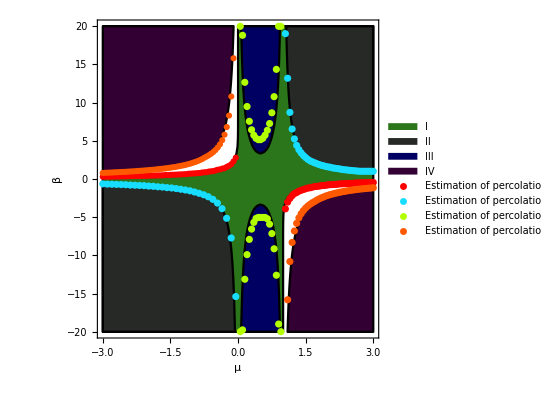

```mathematica
percdt=Show[percplt,dots]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","percdtplt.png"}],percdt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\percdtplt.png

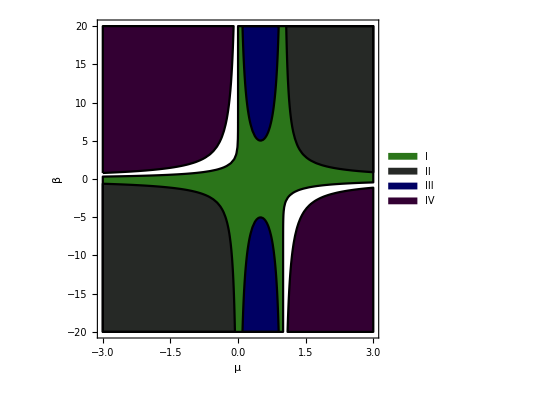

```mathematica
percplt2=RegionPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.59274,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274},{μ,-3,3},{β,-20,20},PlotLegends->{"I","II","III","IV"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotStyle->{RGBColor[0.17,0.46,0.1],RGBColor[0.15,0.16,0.15],RGBColor[0,0,0.39],RGBColor[0.2,0,0.2]},BoundaryStyle->Black]
```

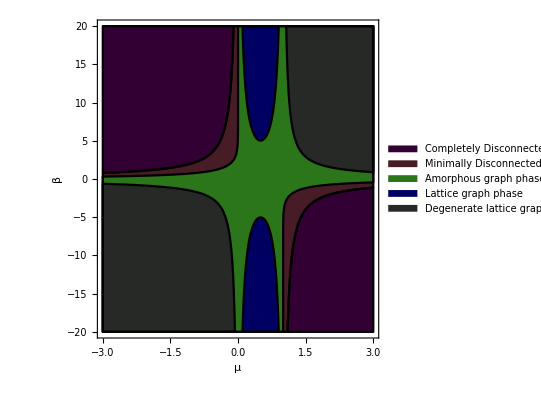

```mathematica
thphaseplt2=RegionPlot[{(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274,Not[(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274||(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274],(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.59274,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407},{μ,-3,3},{β,-20,20},BoundaryStyle->Black,PlotLegends->{"Completely Disconnected phase","Minimally Disconnected phase","Amorphous graph phase","Lattice graph phase","Degenerate lattice graph phase"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotStyle->{RGBColor[0.2,0,0.2],RGBColor[0.28,0.11,0.15],RGBColor[0.17,0.46,0.1],RGBColor[0,0,0.39],RGBColor[0.15,0.16,0.15]}]
```

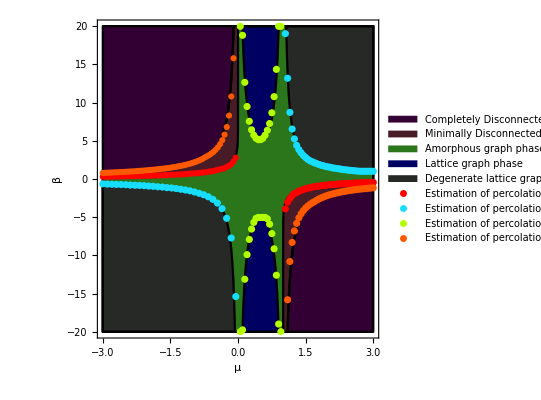

```mathematica
percdt2=Show[thphaseplt2,dots]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","percdtplt2.png"}],percdt2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\percdtplt2.png

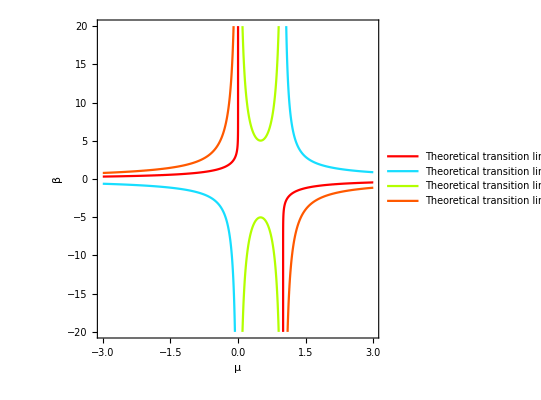

```mathematica
lines=ContourPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4==0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4==0.59274,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4==0.59274},{μ,-3,3},{β,-20,20},AspectRatio->1,
ContourStyle->{Red,RGBColor[0.09,0.87,1],RGBColor[0.7,1,0],RGBColor[1,0.35,0]},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotPoints->100,PlotLegends->{"Theoretical transition line of percolation I","Theoretical transition line of percolation II","Theoretical transition line of percolation III","Theoretical transition line of percolation IV"}]
```

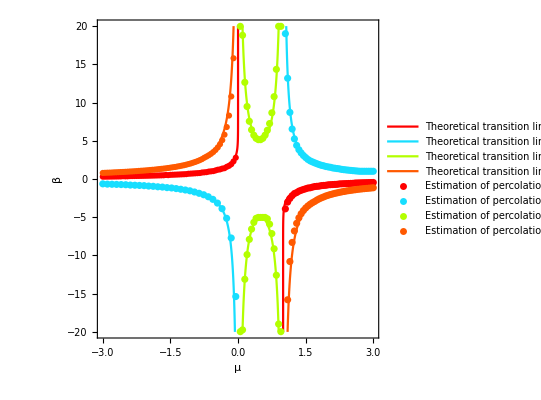

```mathematica
linedtplt=Show[lines,dots]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","linedtplt.png"}],linedtplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\linedtplt.png

## Tearing

```mathematica
RegionPlot[{β μ<0.&&β (μ-1)>0.},{μ,-3,3},{β,-20,20},PlotPoints->200]
```

```mathematica
RegionPlot[{-β μ>2&&(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))>0.5},{μ,-3,3},{β,-20,20},PlotPoints->200]
```

```mathematica
Show[DensityPlot[√(1/(1-1/(1+ⅇ^(β μ)))),{μ,-3,3},{β,-20,20},PlotPoints->100,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"β","μ"}],lines,ImageSize->400]
```

```mathematica
Plot3D[√(1/(1-1/(1+ⅇ^(β μ)))),{μ,-3,3},{β,-20,20},PlotRange->{0,10000}]
```

```mathematica
ContourPlot[√(1/(1-1/(1+ⅇ^(β μ)))),{μ,-3,3},{β,-20,20}]
```

```mathematica
Plot[√(1/(1-1/(1+ⅇ^(-μ^2)))),{μ,-7,7}]
```

```mathematica
FullSimplify[√(1/(1-1/(1+ⅇ^(-μ^2))))]
```

```mathematica
FullSimplify[√(1/(1-1/(1+ⅇ^(β μ))))]
```

## Graph Diameters

```mathematica
(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2/.μ->-β
```

1/2 (2-1/(1+ⅇ^(-β^2))-ⅇ^β/(ⅇ^β+ⅇ^(-β^2)))

```mathematica
FindRoot[1/2 (2-1/(1+ⅇ^(-β^2))-ⅇ^β/(ⅇ^β+ⅇ^(-β^2)))==0.250368,{β,0.8}]
```

{β→0.84732}

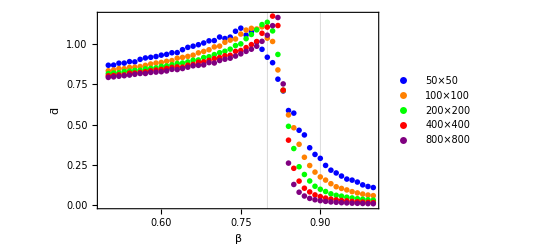

```mathematica
ListPlot[{First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams50.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams100.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams200.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams400.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams800.csv"}]]},DataRange->{0.5,1},Frame->True,FrameLabel->{"β","d̄"},ImageSize->400,PlotMarkers->{"OpenMarkers", Small},PlotLegends->{"50×50","100×100","200×200","400×400","800×800"},PlotStyle->{Blue,Orange,Green,Red,Purple},GridLines->{{0.8,0.9},{}},LabelStyle->Directive[Bold,16]]
```

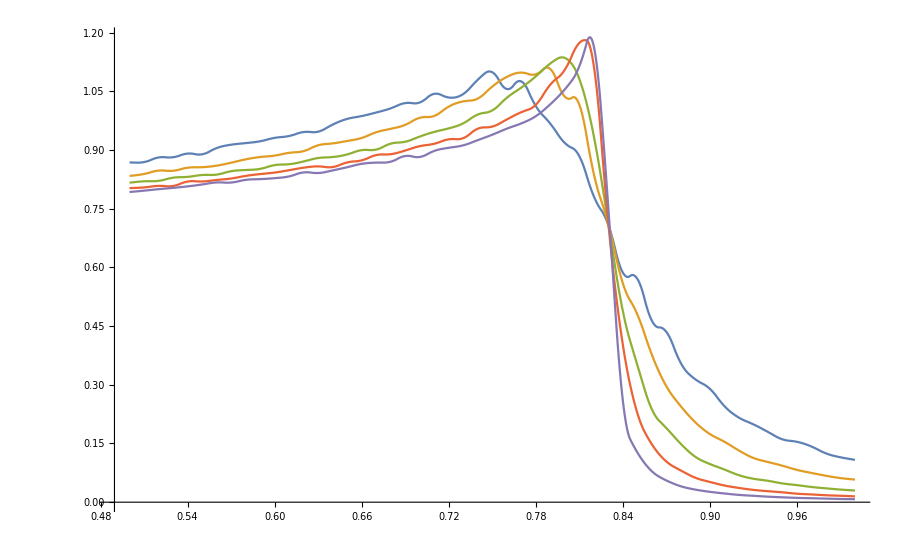

```mathematica
ListLinePlot[{First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams50.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams100.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams200.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams400.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams800.csv"}]]},DataRange->{0.5,1},InterpolationOrder->2]
```

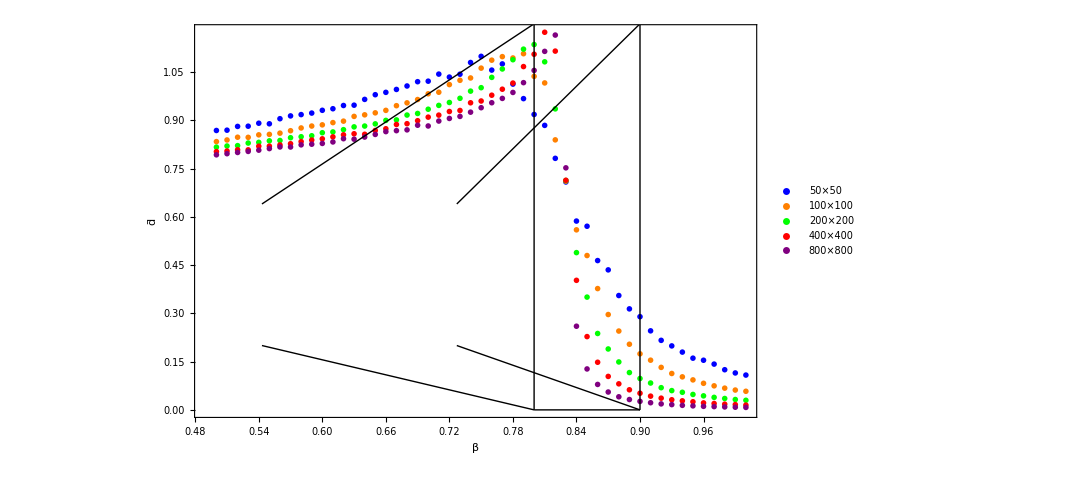

```mathematica
grdsts=Show[ListPlot[{First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams50.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams100.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams200.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams400.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams800.csv"}]]},DataRange->{0.5,1},Frame->True,FrameLabel->{"β","d̄"},ImageSize->800,PlotMarkers->{"OpenMarkers", Small},PlotLegends->{"50×50","100×100","200×200","400×400","800×800"},PlotStyle->{Blue,Orange,Green,Red,Purple},LabelStyle->Directive[Bold,16],Prolog->Inset[Show[ListPlot[{First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams2_50.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams2_100.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams2_200.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams2_400.csv"}]],First@Transpose@Import[FileNameJoin[{NotebookDirectory[],"graphDiams2_800.csv"}]]},DataRange->{0.8,0.9},Frame->True,PlotMarkers->{"OpenMarkers", Small},PlotStyle->{Blue,Orange,Green,Red,Purple},PlotRange->{0.0,1.25}]],{0.55,0.2},{0.8,0.},0.2]],Graphics[{Thin,Line[{{0.8,1.2},{0.9,1.2}}],Line[{{0.9,1.2},{0.9,0}}],Line[{{0.9,0},{0.8,0}}],Line[{{0.8,0},{0.8,1.2}}],Line[{{0.543,0.64},{0.8,1.2}}],Line[{{0.727,0.64},{0.9,1.2}}],Line[{{0.543,0.2},{0.8,0.0}}],Line[{{0.727,0.2},{0.9,0.0}}]}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","grdsts.png"}],grdsts]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\grdsts.png

### Junk

```mathematica
GraphDiameter[Subgraph[#,First@ConnectedComponents[#]]]&[Graph[Import[FileNameJoin[{NotebookDirectory[],"graphs","100","0.0","-0.0","1.el"}]]]]
```

```mathematica
AbsoluteTiming[GraphDiameter[Subgraph[#,First@ConnectedComponents[#]]]&[Graph[Import[FileNameJoin[{NotebookDirectory[],"graphs","100","0.0","-0.0","1.el"}]]]]]
```

```mathematica
names=FileNames[All,FileNameJoin[{NotebookDirectory[],"graphs","100",ToString[#],ToString[-#]}]]&/@Range[0.5,1,0.05];
```

```mathematica
Length[names]
```

```mathematica
AbsoluteTiming[GraphDiameter[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names[[2]][[5]]]]]
```

```mathematica
AbsoluteTiming[N@MeanGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names[[2]][[5]]]]]
```

```mathematica
RandomChoice[{1,2,3},{2,10}]
```

```mathematica
MeanAroundGraphDistance[graph_]:=N@MeanAround[GraphDistance[graph,#1,#2]&@@@RandomChoice[VertexList[graph],{1000,2}]]
```

```mathematica
AbsoluteTiming[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names[[2]][[5]]]]]
```

```mathematica
1.3*128*10/8
```

```mathematica
AbsoluteTiming[dt=MeanAround[ParallelMap[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[#]]&,#]]&/@names;]
```

```mathematica
ListPlot[dt,DataRange->{0.5,1}]
```

```mathematica
Speak["Done"]
Speak["Done"]
Speak["Done"]
Speak["Done"]
```

```mathematica
names2=FileNames[All,FileNameJoin[{NotebookDirectory[],"graphs","200",ToString[#],ToString[-#]}]]&/@Range[0.5,1,0.05];
```

```mathematica
Length[names2]
```

```mathematica
AbsoluteTiming[GraphDiameter[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names2[[2]][[5]]]]]
```

```mathematica
195.58*128*10/8/60
```

```mathematica
AbsoluteTiming[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names2[[2]][[5]]]]]
```

```mathematica
0.76*128*11/8
```

```mathematica
AbsoluteTiming[dt2=MeanAround[ParallelMap[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[#]]&,#]]&/@names2;]
```

```mathematica
ListPlot[dt2,DataRange->{0.5,1}]
```

```mathematica
mg1=N@MeanGraphDistance[GridGraph[{100,100}]]
mg2=N@MeanGraphDistance[GridGraph[{200,200}]]
```

```mathematica
ListPlot[{dt/mg1,dt2/mg2},DataRange->{0.5,1}]
```

```mathematica
names3=FileNames[All,FileNameJoin[{NotebookDirectory[],"graphs","300",ToString[#],ToString[-#]}]]&/@Range[0.5,1,0.05];
```

```mathematica
AbsoluteTiming[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[names3[[2]][[5]]]]]
```

```mathematica
AbsoluteTiming[dt3=MeanAround[ParallelMap[MeanAroundGraphDistance[Subgraph[#,First@ConnectedComponents[#]]]&@Graph[Import[#]]&,#]]&/@names3;]
```

```mathematica
mg3=N@MeanGraphDistance[GridGraph[{300,300}]]
```

```mathematica
mg2/mg1
```

```mathematica
ListPlot[{dt/mg1,dt2/(2*mg1),dt3/(3*mg1)},DataRange->{0.5,1},PlotMarkers->{Automatic, Small}]
```

```mathematica
FullSimplify[1/Sin[x]^2-Cos[x]^2/Sin[x]^2-1]
FullSimplify[1/Sin[x]^2-2 Cos[x]^2/Sin[x]^2]
```

```mathematica
D[Sin[x]Cos[x],x]
```

```mathematica
DSolve[v'[r]==Subscript[r, g]/r 1/(r-Subscript[r, g]),v[r],r]
```

## Degree Distribution Entropy

```mathematica
dentrplt=Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","dentrplt.png"}],dentrplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\dentrplt.png

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"normEntropy.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v/𝓈",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
N@Tanh[1]
```

0.761594

```mathematica
entrDt=Table[β+(ⅇ^β β (-1.+μ))/(ⅇ^β+ⅇ^(β μ))+(-2.+1./(1+ⅇ^(β μ))) β μ+Log[1.+ⅇ^(β (-1+μ))]+Log[1.+ⅇ^(β μ)],{μ,-3,3,6/50},{β,-20,20,40/50}];
```

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","gentrplt.png"}],gentrplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\gentrplt.png

### Info Th jnk

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-Transpose@entrDt,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v-S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Show[ListDensityPlot[#/Max[Flatten[#]]&@Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-#/Max[Flatten[#]]&@Transpose@entrDt,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v-S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Show[ListDensityPlot[Abs[#/Mean[Flatten[#]]&@Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-#/Mean[Flatten[#]]&@Transpose@entrDt]/400,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v-S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
ListPlot3D[Abs[#/Mean[Flatten[#]]&@Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-#/Mean[Flatten[#]]&@Transpose@entrDt]/2,PlotRange->All]
```

```mathematica
ListPlot3D[#/Max[Flatten[#]]&@Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-#/Max[Flatten[#]]&@Transpose@entrDt]
```

```mathematica
dl[β_,μ_,n_]:=RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ)])],n]+RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ-1)])],n]
```

```mathematica
AbsoluteTiming[entrDt2=Table[Entropy[dl[β,μ,100000]],{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{14.5057,Null}

```mathematica
Show[ListDensityPlot[Transpose@entrDt2,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Show[DensityPlot[β+(ⅇ^β β (-1.+μ))/(ⅇ^β+ⅇ^(β μ))+(-2.+1./(1+ⅇ^(β μ))) β μ+Log[1.+ⅇ^(β (-1+μ))]+Log[1.+ⅇ^(β μ)],{μ,-3,3},{β,-20,20},PlotPoints->100,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"β","μ"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]-Transpose@entrDt2,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_v-S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Integrate[Exp[-ϵ k],k]
```

```mathematica
entrDt3=Table[β+(ⅇ^β β (-1.+μ))/(ⅇ^β+ⅇ^(β μ))+(-2.+1./(1+ⅇ^(β μ))) β μ+Log[1.+ⅇ^(β (-1+μ))]+Log[1.+ⅇ^(β μ)],{μ,-3,3,0.05},{β,-10,10,0.25}];
AbsoluteTiming[entrDt4=ParallelTable[Entropy[dl[β,μ,1000]],{μ,-3,3,0.05},{β,-10,10,0.25}];]
```

```mathematica
ListPlot3D[Abs[#/Mean[Flatten[#]]&@entrDt4-#/Mean[Flatten[#]]&@entrDt3]]
```

```mathematica
dl2[β_,μ_,n_]:=Module[{p1=Mean[RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ)])],n]]/8,p2=Mean[RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ-1)])],n]]/8},{1-p1-p2,p1,p2}]
```

```mathematica
Mean[BinomialDistribution[4,1-1/(1+Exp[β(μ)])]]
Mean[BinomialDistribution[4,1-1/(1+Exp[β(μ-1)])]]
```

```mathematica
FullSimplify[-(Log[(1-1/(1+ⅇ^(β μ)))/2](1-1/(1+ⅇ^(β μ)))/2+Log[(1-1/(1+ⅇ^(β (-1+μ))))/2](1-1/(1+ⅇ^(β (-1+μ))))/2+Log[1-((1-1/(1+ⅇ^(β μ)))+(1-1/(1+ⅇ^(β (-1+μ)))))/2](1-((1-1/(1+ⅇ^(β μ)))+(1-1/(1+ⅇ^(β (-1+μ)))))/2))/Log[ⅇ]]
```

```mathematica
Show[DensityPlot[-((ⅇ^(β μ)+ⅇ^(β (-1+2 μ))) Log[1/(2+2 ⅇ^(-β μ))]+ⅇ^(β (-1+μ)) (1+ⅇ^(β μ)) Log[1/(2+2 ⅇ^(β-β μ))]+(2+ⅇ^(β (-1+μ))+ⅇ^(β μ)) Log[1/2 (1/(1+ⅇ^(β (-1+μ)))+1/(1+ⅇ^(β μ)))])/(2 (1+ⅇ^(β (-1+μ))) (1+ⅇ^(β μ))),{μ,-3,3},{β,-20,20},PlotPoints->100,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"β","μ"}],lines,ImageSize->400]
```

```mathematica
Show[DensityPlot[(β+(ⅇ^β β (-1.+μ))/(ⅇ^β+ⅇ^(β μ))+(-2.+1./(1+ⅇ^(β μ))) β μ+Log[1.+ⅇ^(β (-1+μ))]+Log[1.+ⅇ^(β μ)])-(-((ⅇ^(β μ)+ⅇ^(β (-1+2 μ))) Log[1/(2+2 ⅇ^(-β μ))]+ⅇ^(β (-1+μ)) (1+ⅇ^(β μ)) Log[1/(2+2 ⅇ^(β-β μ))]+(2+ⅇ^(β (-1+μ))+ⅇ^(β μ)) Log[1/2 (1/(1+ⅇ^(β (-1+μ)))+1/(1+ⅇ^(β μ)))])/(2 (1+ⅇ^(β (-1+μ))) (1+ⅇ^(β μ)))),{μ,-3,3},{β,-20,20},PlotPoints->100,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"β","μ"}],lines,ImageSize->400]
```

```mathematica
FullSimplify[a/(a+b)Log[a/(a+b)]+b/(a+b)Log[b/(a+b)],Assumptions->0<a<1&&0<b<1]
```

```mathematica
Limit[(a Log[a/(a+b)]+b Log[b/(a+b)])/(a+b),{a->0,b->0}]
```

```mathematica
FullSimplify[-a/(a+b)Log[a/(a+b)]-b/(a+b)Log[b/(a+b)]/.{a->4 (1-1/(1+ⅇ^(β μ))),b->4 (1-1/(1+ⅇ^(β (-1+μ))))}]
```

```mathematica
Show[DensityPlot[-((ⅇ^β+ⅇ^(β μ)) Log[(ⅇ^β+ⅇ^(β μ))/(1+ⅇ^β+2 ⅇ^(β μ))]+(1+ⅇ^(β μ)) Log[1/(2+(-1+ⅇ^β)/(1+ⅇ^(β μ)))])/(1+ⅇ^β+2 ⅇ^(β μ)),{μ,-3,3},{β,-20,20},PlotPoints->100,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"β","μ"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
entrDt2=Table[-((ⅇ^β+ⅇ^(β μ)) Log[(ⅇ^β+ⅇ^(β μ))/(1+ⅇ^β+2 ⅇ^(β μ))]+(1+ⅇ^(β μ)) Log[1/(2+(-1+ⅇ^β)/(1+ⅇ^(β μ)))])/(1+ⅇ^β+2 ⅇ^(β μ)),{μ,-3,3,6/50},{β,-20,20,40/50}];
```

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"entropy.csv"}]]+Transpose@entrDt2-Transpose@entrDt,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_G",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

## Geometry

```mathematica
mndgplt=Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"meanDegree.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","mndgplt.png"}],mndgplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\mndgplt.png

```mathematica
clsplt=Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"meanLocalClusteringCoef.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"(C̄)_ℓ",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","clsplt.png"}],clsplt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass3\Report\figures\clsplt.png

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","dentrplt.png"}],dentrplt]
```

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"globalClusteringCoef.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"(C̄)_ℓ",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"poissonEntropy.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S_p",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Boole[3.2<#<4.8]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"meanDegree.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Boole[0.1<#]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"meanLocalClusteringCoef.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"(C̄)_ℓ",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Boole[0.3<#]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"poissonEntropy.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"(C̄)_ℓ",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListContourPlot[(Boole[3.<#<5.]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"meanDegree.csv"}]])*(Boole[0.1<#]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"meanLocalClusteringCoef.csv"}]])*(Boole[0.3<#]&/@#&/@Import[FileNameJoin[{NotebookDirectory[],"poissonEntropy.csv"}]]),DataRange->{{-3,3},{-20,20}},ColorFunction->"CherryTones",LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

## Big Comps

Show::gcomb: Could not combine the graphics objects in Show[,lines,ImageSize→400].

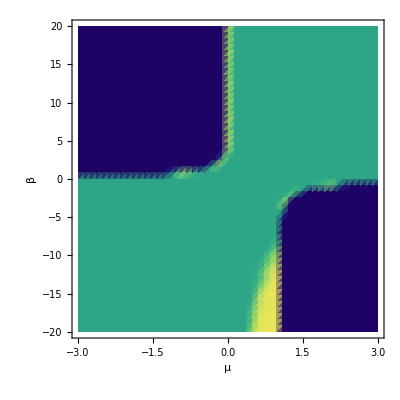
Show[-Graphics-,lines,ImageSize→400]

Show::gcomb: Could not combine the graphics objects in Show[,lines,ImageSize→400].

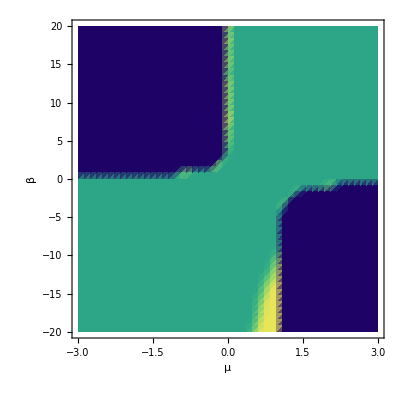
Show[-Graphics-,lines,ImageSize→400]

Show::gcomb: Could not combine the graphics objects in Show[,lines,ImageSize→400].

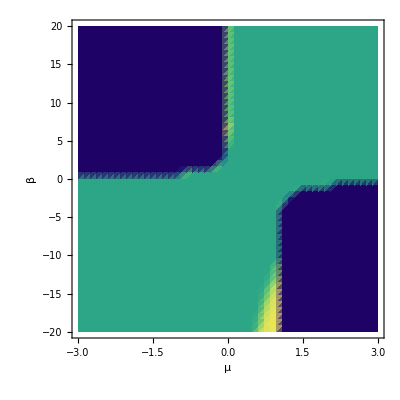
Show[-Graphics-,lines,ImageSize→400]

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"numBigComps50.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"numBigComps100.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"numBigComps200.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

```mathematica
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"numBigComps50.csv"}]]-Import[FileNameJoin[{NotebookDirectory[],"numBigComps100.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
Show[ListDensityPlot[Import[FileNameJoin[{NotebookDirectory[],"numBigComps100.csv"}]]-Import[FileNameJoin[{NotebookDirectory[],"numBigComps200.csv"}]],DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"D̄",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

## Partition function

```mathematica
-D[-(Log[1+Exp[β μ]]+Log[1+Exp[β(μ-1)]])/β,μ]
```

((ⅇ^(β (-1+μ)) β)/(1+ⅇ^(β (-1+μ)))+(ⅇ^(β μ) β)/(1+ⅇ^(β μ)))/β

```mathematica
FullSimplify[((ⅇ^(β (-1+μ)) β)/(1+ⅇ^(β (-1+μ)))+(ⅇ^(β μ) β)/(1+ⅇ^(β μ)))/β]
```

2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ))

```mathematica
D[1/T,T]
```

-1/T^2

```mathematica
β^2 D[-(Log[1+Exp[β μ]]+Log[1+Exp[β(μ-1)]])/β,β]
```

β^2 (-((ⅇ^(β (-1+μ)) (-1+μ))/(1+ⅇ^(β (-1+μ)))+(ⅇ^(β μ) μ)/(1+ⅇ^(β μ)))/β+(Log[1+ⅇ^(β (-1+μ))]+Log[1+ⅇ^(β μ)])/β^2)

```mathematica
FullSimplify[β^2 (-((ⅇ^(β (-1+μ)) (-1+μ))/(1+ⅇ^(β (-1+μ)))+(ⅇ^(β μ) μ)/(1+ⅇ^(β μ)))/β+(Log[1+ⅇ^(β (-1+μ))]+Log[1+ⅇ^(β μ)])/β^2)]
```

β+(ⅇ^β β (-1+μ))/(ⅇ^β+ⅇ^(β μ))+(-2+1/(1+ⅇ^(β μ))) β μ+Log[1+ⅇ^(β (-1+μ))]+Log[1+ⅇ^(β μ)]

## EOS

```mathematica
Solve[n/V==2-1/(1+Exp[β μ])-1/(1+Exp[β (μ-1)]),μ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→Log[(-n-ⅇ^β n+V+ⅇ^β V-√(4 ⅇ^β n (-n+2 V)+(-n-ⅇ^β n+V+ⅇ^β V)^2))/(2 (n-2 V))]/β},{μ→Log[(-n-ⅇ^β n+V+ⅇ^β V+√(4 ⅇ^β n (-n+2 V)+(-n-ⅇ^β n+V+ⅇ^β V)^2))/(2 (n-2 V))]/β}}

```mathematica
FullSimplify[Log[(-n-ⅇ^β n+V+ⅇ^β V-√(4 ⅇ^β n (-n+2 V)+(-n-ⅇ^β n+V+ⅇ^β V)^2))/(2 (n-2 V))]/β/.β->1/T,Assumptions->V>0&&n>0&&T>0]
```

T Log[-((1+ⅇ^(1/T)) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-(1+ⅇ^(1/T)) V)/(2 (n-2 V))]

```mathematica
FullSimplify[P==T(Log[1+Exp[μ/T]]+Log[1+Exp[(μ-1)/T]])/.μ->T Log[-((1+ⅇ^(1/T)) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-(1+ⅇ^(1/T)) V)/(2 (n-2 V))],Assumptions->V>0&&n>0&&T>0]
```

1+P==T (Log[-(n-ⅇ^(1/T) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-V+3 ⅇ^(1/T) V)/(2 (n-2 V))]+Log[1-((1+ⅇ^(1/T)) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-(1+ⅇ^(1/T)) V)/(2 (n-2 V))])

```mathematica
Asymptotic[T (Log[-(n-ⅇ^(1/T) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-V+3 ⅇ^(1/T) V)/(2 (n-2 V))]+Log[1-((1+ⅇ^(1/T)) n+√(-4 ⅇ^(1/T) n (n-2 V)+(1+ⅇ^(1/T))^2 (n-V)^2)-(1+ⅇ^(1/T)) V)/(2 (n-2 V))]),V->Infinity,Assumptions->V>0&&n>0&&T>0]
```

1

```mathematica
FullSimplify[(n T (V+ⅇ^(1/T) V-√((1+ⅇ^(1/T))^2 V^2)) (V+3 ⅇ^(1/T) V+3 ⅇ^(2/T) V+ⅇ^(3/T) V+√((1+ⅇ^(1/T))^2 V^2)-6 ⅇ^(1/T) √((1+ⅇ^(1/T))^2 V^2)+ⅇ^(2/T) √((1+ⅇ^(1/T))^2 V^2)))/((1+ⅇ^(1/T))^2 V (V-3 ⅇ^(1/T) V+√((1+ⅇ^(1/T))^2 V^2)) (-3 V+ⅇ^(1/T) V+√((1+ⅇ^(1/T))^2 V^2)))+T (Log[(-V+3 ⅇ^(1/T) V-√((1+ⅇ^(1/T))^2 V^2))/(2 V)]+Log[-(-3 V+ⅇ^(1/T) V+√((1+ⅇ^(1/T))^2 V^2))/(2 V)]),Assumptions->V>0&&n>0&&T>0]
```

T Log[-(-1+ⅇ^(1/T))^2]

```mathematica
P==0 for n<<V
```

```mathematica
Solve[1==2-1/(1+Exp[β μ])-1/(1+Exp[β (μ-1)]),μ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→1/2}}

```mathematica
FullSimplify[P==T(Log[1+Exp[μ/T]]+Log[1+Exp[(μ-1)/T]])/.μ->1/2,Assumptions->V>0&&n>0&&T>0]
```

P==T Log[4 Cosh[1/(4 T)]^2]

```mathematica
P≈2T Log[2Cosh[1/(4 T)]] for n≈V
```

```mathematica
Asymptotic[T Log[4 Cosh[1/(4 T)]^2],T->Infinity]
```

T Log[4]

```mathematica
P==2Log[2]T for n=V and T>>1
```

```mathematica
Solve[2==2-1/(1+Exp[β μ])-1/(1+Exp[β (μ-1)]),μ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→-Log[1/2 (-1-ⅇ^-β)]/β}}

```mathematica
FullSimplify[-Log[1/2 (-1-ⅇ^-β)]/β/.β->1/T,Assumptions->V>0&&n>0&&T>0]
```

-T Log[1/2 (-1-ⅇ^(-1/T))]

```mathematica
FullSimplify[P==T(Log[1+Exp[μ/T]]+Log[1+Exp[(μ-1)/T]])/.μ->-T Log[1/2 (-1-ⅇ^(-1/T))],Assumptions->T>0]
```

P==T Log[-Tanh[1/(2 T)]^2]

```mathematica
Asymptotic[P==T Log[-Tanh[1/(2 T)]^2],T->0]
```

P==T Log[-Tanh[1/(2 T)]^2]

## Information Theory

```mathematica
dl[β_,μ_,n_]:=Transpose[{RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ)])],n],RandomVariate[BinomialDistribution[4,1-1/(1+Exp[β(μ-1)])],n]}]
dl2[β_,μ_,n_]:=(#1+#2)&@@@dl[β,μ,n]
```

```mathematica
AbsoluteTiming[entrDt2=ParallelTable[Entropy[4*#1+#2&@@@dl[β,μ,10000]],{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{6.12077,Null}

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt2,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
AbsoluteTiming[entrDt3=ParallelTable[Entropy[(#1+#2)&@@@dl[β,μ,10000]],{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{4.76606,Null}

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt3,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
AbsoluteTiming[entrDt32=ParallelTable[Entropy[32.,N[#1*#2]&@@@dl[β,μ,10000]],{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{5.63044,Null}

```mathematica
Max[Flatten@entrDt32]
```

0.611504

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt32,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt4-Transpose@entrDt32,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
Solve[a==x+y&&b==x/(x+y),{x,y}]
```

{{x→a b,y→a-a b}}

```mathematica
FullSimplify[Log[(1-1/(1+Exp[β(μ)]))/(1-1/(1+Exp[β(μ)])+1-1/(1+Exp[β(μ-1)]))]((1-1/(1+Exp[β(μ)]))/(1-1/(1+Exp[β(μ)])+1-1/(1+Exp[β(μ-1)])))+Log[1-(1-1/(1+Exp[β(μ)]))/(1-1/(1+Exp[β(μ)])+1-1/(1+Exp[β(μ-1)]))](1-(1-1/(1+Exp[β(μ)]))/(1-1/(1+Exp[β(μ)])+1-1/(1+Exp[β(μ-1)])))]
```

((ⅇ^β+ⅇ^(β μ)) Log[(ⅇ^β+ⅇ^(β μ))/(1+ⅇ^β+2 ⅇ^(β μ))]+(1+ⅇ^(β μ)) Log[1/(2+(-1+ⅇ^β)/(1+ⅇ^(β μ)))])/(1+ⅇ^β+2 ⅇ^(β μ))

```mathematica
AbsoluteTiming[entrDt4=ParallelTable[-((ⅇ^β+ⅇ^(β μ)) Log[(ⅇ^β+ⅇ^(β μ))/(1+ⅇ^β+2 ⅇ^(β μ))]+(1+ⅇ^(β μ)) Log[1/(2+(-1+ⅇ^β)/(1+ⅇ^(β μ)))])/(1+ⅇ^β+2 ⅇ^(β μ)),{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{0.017611,Null}

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt4,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
AbsoluteTiming[entrDt5=ParallelTable[Abs[Log[1-1/(1+Exp[β(μ)])](1-1/(1+Exp[β(μ)]))+Log[(1-1/(1+Exp[β(μ-1)]))](1-1/(1+Exp[β(μ-1)]))+Log[1/(1+Exp[β(μ)])] 1/(1+Exp[β(μ)])+Log[1/(1+Exp[β(μ-1)])] 1/(1+Exp[β(μ-1)])],{μ,-3,3,0.1},{β,-20,20,0.5}];]
```

{0.0483026,Null}

```mathematica
gentrplt=Show[ListDensityPlot[Transpose@entrDt5,DataRange->{{-3,3},{-20,20}},ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"S",LabelStyle->Directive[Bold,16],LegendMarkerSize->360],{0.54,1.}],LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"}],lines,ImageSize->400]
```

-Graphics-

```mathematica
entrDt5[[20]][[30]]
```

(9894 Log[2]+106 Log[7/3])/10000

```mathematica
dl[0,0,3]
```

{{2,1},{2,1},{3,3}}

## Measureables

```mathematica
FullSimplify[d==4(2-1/(1+ⅇ^(β μ))-1/(1+ⅇ^(β (μ-1))))/.{β->1/T,μ->T Log[1/2 (-1-ⅇ^(1/T)+√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]}]
```

d==-2 ⅇ^(-(1+P)/T) (-1+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)+ⅇ^(1/T) (2-ⅇ^(1/T)-4 ⅇ^(P/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)))

```mathematica
FullSimplify[Normal@Series[Normal@Series[-2 ⅇ^(-(1+P)/T) (-1+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)+ⅇ^(1/T) (2-ⅇ^(1/T)-4 ⅇ^(P/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))),{P,0,1}],{T,0,1}]]
```

(2 ⅇ^(-1/T) (P-√((1+ⅇ^(1/T))^2) P+ⅇ^(1/T) (1+2 √((1+ⅇ^(1/T))^2)+ⅇ^(1/T) (1+ⅇ^(1/T)-√((1+ⅇ^(1/T))^2))) P+(1+ⅇ^(1/T))^2 (-1-ⅇ^(1/T)+√((1+ⅇ^(1/T))^2)) T))/(√((1+ⅇ^(1/T))^2) T)

```mathematica
Clear[v]
```

```mathematica
FullSimplify[v==4((1-1/(1+ⅇ^(β μ)))1/(1+ⅇ^(β μ))+(1-1/(1+ⅇ^(β (μ-1))))1/(1+ⅇ^(β (μ-1))))/.{β->1/T,μ->T Log[1/2 (-1-ⅇ^(1/T)+√(1+4 ⅇ^(1/T+P/T)-2 ⅇ^(1/T)+ⅇ^(2/T)))]}]
```

v==8 ((-1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))/((1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)-(2 ⅇ^(2/T))/((-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)+ⅇ^(1/T)/(-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)))

```mathematica
FullSimplify[Normal@Series[Normal@Series[8 ((-1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))/((1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)-(2 ⅇ^(2/T))/((-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)+ⅇ^(1/T)/(-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))),{P,0,1}],{T,0,1}]]
```

(ⅇ^(-2/T) (2 (-2+2 √((1+ⅇ^(1/T))^2)-ⅇ^(1/T) (1+√((1+ⅇ^(1/T))^2)+ⅇ^(1/T) (-1-2 √((1+ⅇ^(1/T))^2)-ⅇ^(1/T) (-1+2 ⅇ^(1/T)) (-1-ⅇ^(1/T)+√((1+ⅇ^(1/T))^2))))) P-2 (1+ⅇ^(1/T))^2 (1+ⅇ^(1/T) (-1+ⅇ^(1/T))) (-1-ⅇ^(1/T)+√((1+ⅇ^(1/T))^2)) T))/(√((1+ⅇ^(1/T))^2) T)

```mathematica
Solve[d==-2 ⅇ^(-(1+P)/T) (-1+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)+ⅇ^(1/T) (2-ⅇ^(1/T)-4 ⅇ^(P/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2)))&&v==8 ((-1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))/((1-ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)-(2 ⅇ^(2/T))/((-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))^2)+ⅇ^(1/T)/(-1+ⅇ^(1/T)+√(4 ⅇ^((1+P)/T)+(-1+ⅇ^(1/T))^2))),{P,T},Assumptions->T>0&&P>0]
```

{}

```mathematica
Select[FullSimplify[Solve[d==4(2-1/(1+ⅇ^(β μ))-1/(1+ⅇ^(β (μ-1))))&&v==Sech[1/2 β (-1+μ)]^2+Sech[(β μ)/2]^2,{β,μ}]/.{C[1]->0,C[2]->0},Assumptions->0<=d<=8&&v>0],Total[Abs@Im[({β,μ}/.#)/.{d->3.9,v->20}]]<0.1&]
```

{}

```mathematica
{β,μ}/.{β->Log[((-4+d) d+4 v) ((-12+d) d+4 (8+v))]-Log[-16 d^3+d^4-64 d (-2+√(-((-8+d) d)-8 v)+v)+8 d^2 (6+√(-((-8+d) d)-8 v)+v)+16 v (-8+2 √(-((-8+d) d)-8 v)+v)],μ->Log[(8 d-d^2+4 √(-((-8+d) d)-8 v)-4 v)/((-12+d) d+4 (8+v))]/(Log[((-4+d) d+4 v) ((-12+d) d+4 (8+v))]-Log[-16 d^3+d^4-64 d (-2+√(-((-8+d) d)-8 v)+v)+8 d^2 (6+√(-((-8+d) d)-8 v)+v)+16 v (-8+2 √(-((-8+d) d)-8 v)+v)])}/.{d->3.9,v->20}
```

{0.-1.28689 ⅈ,-1.94124-0.0038849 ⅈ}

```mathematica
E
```